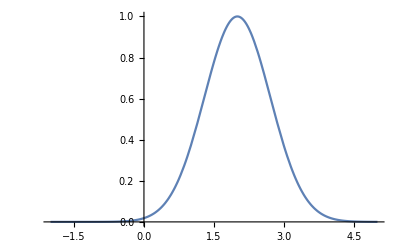

1.77245

```mathematica
f[x_]:=Exp[-(x-a)^2];                                                    (*Not normalized*)
a=2;
Plot[f[x],{x,-2,5},PlotRange->Full,PlotLegends->"Expressions"]
NIntegrate[f[x],{x,-∞,∞}]
```

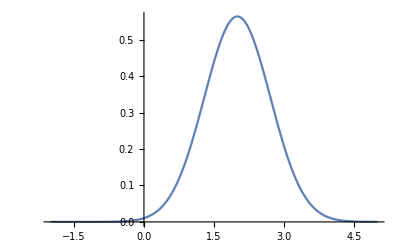

1.

```mathematica
f[x_]:=(1/Sqrt[π])*Exp[-(x-a)^2];                        (*Normalized*)
a=2;
Plot[f[x],{x,-2,5},PlotRange->Full,PlotLegends->"Expressions"]
NIntegrate[f[x],{x,-∞,∞}]
```

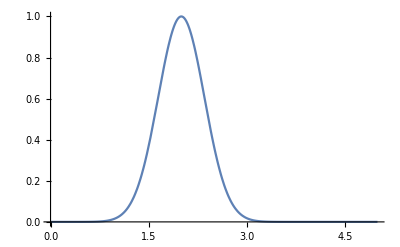

0.886227

1.77245

```mathematica
f[x_,k_]:=Exp[-((x-a)^2)/k^2];                                     (*Not normalized*) (*What do k do in the exponential*)
a=2;
Plot[f[x,k=0.5],{x,0,5},PlotRange->Full,PlotLegends->"Expressions"]
NIntegrate[f[x,k=0.5],{x,-∞,∞}]
2*NIntegrate[f[x,k=0.5],{x,-∞,∞}]
```

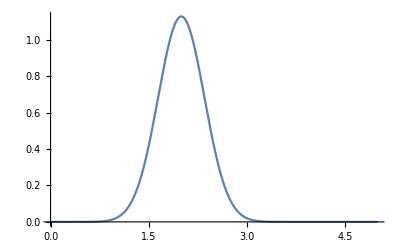

1.

1.

```mathematica
f[x_,k_]:=(1/(k Sqrt[π]))Exp[-((x-a)^2)/k^2];                         (*Normalized*)
a=2;
Plot[f[x,k=0.5],{x,0,5},PlotRange->Full,PlotLegends->"Expressions"]
NIntegrate[f[x,k=0.5],{x,-∞,∞}]
NIntegrate[f[x,k=0.05],{x,-∞,∞}]
```

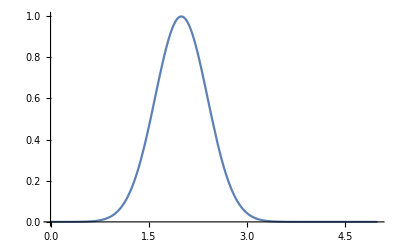

```mathematica
G[x_]:=(1/(σ*Sqrt[2Pi]))Exp[-((x-a)^2)/(2σ^2)];         (*What do σ do in the exponenetial*)
a=2;σ=0.4;
Plot[G[x], {x, 0,5}]
```

General::munfl: Exp[-799.918] is too small to represent as a normalized machine number; precision may be lost.

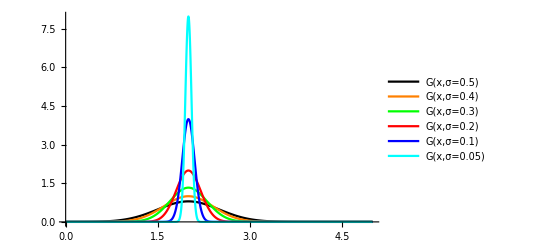

1.

1.

```mathematica
G[x_, σ_]:=(1/(σ*Sqrt[2Pi]))Exp[-((x-a)^2)/(2σ^2)];     (*What do σ do in the exponenetial*)
a=2;
Plot[{G[x, σ=0.5],G[x, σ=0.4],G[x, σ=0.3],G[x, σ=0.2],G[x, σ=0.1],G[x, σ=0.05]},{x, 0,5}, PlotRange->Full,PlotStyle->{Black,Orange,Green,Red,Blue,Cyan}, PlotLegends->"Expressions"]
NIntegrate[G[x,σ=0.5],{x,-∞, ∞}]
NIntegrate[G[x,σ=0.05],{x,-∞, ∞}]
```

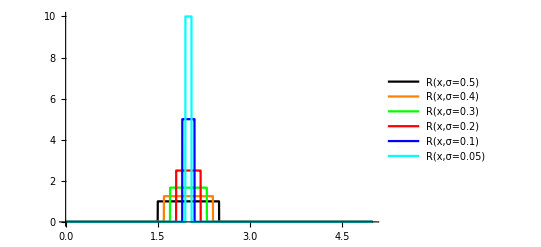

1.

1.

```mathematica
R[x_,σ_]:=Piecewise[{{1/(2σ),-σ<x-a<σ},{0,Modulus[x-a]>σ}}];
a=2;
Plot[{R[x,σ=0.5],R[x,σ=0.4],R[x,σ=0.3],R[x,σ=0.2],R[x,σ=0.1],R[x,σ=0.05]},{x,0,5},PlotRange->Full,PlotStyle->{Black,Orange,Green,Red,Blue,Cyan},PlotLegends->"Expressions"]
NIntegrate[R[x,σ=0.5],{x,-∞, ∞}]
NIntegrate[R[x,σ=0.05],{x,-∞, ∞}]
```

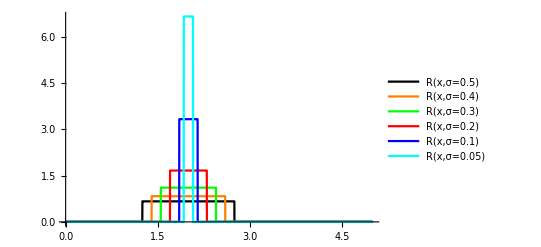

1.

1.

```mathematica
R[x_,σ_]:=Piecewise[{{1/(3σ),-3σ/2<x-a<3σ/2},{0,Modulus[x-a]>3σ/2}}];
a=2;
Plot[{R[x,σ=0.5],R[x,σ=0.4],R[x,σ=0.3],R[x,σ=0.2],R[x,σ=0.1],R[x,σ=0.05]},{x,0,5},PlotRange->Full,PlotStyle->{Black,Orange,Green,Red,Blue,Cyan},PlotLegends->"Expressions"]
NIntegrate[R[x,σ=0.5],{x,-∞, ∞}]
NIntegrate[R[x,σ=0.05],{x,-∞, ∞}]
```

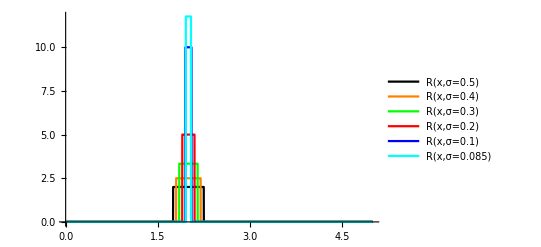

1.

1.

```mathematica
R[x_,σ_]:=Piecewise[{{1/σ,-σ/2<x-a<σ/2},{0,Modulus[x-a]>σ/2}}];
a=2;
Plot[{R[x,σ=0.5],R[x,σ=0.4],R[x,σ=0.3],R[x,σ=0.2],R[x,σ=0.1],R[x,σ=0.085]},{x,0,5},PlotRange->Full,PlotStyle->{Black,Orange,Green,Red,Blue,Cyan},PlotLegends->"Expressions"]
NIntegrate[R[x,σ=0.5],{x,-∞, ∞}]
NIntegrate[R[x,σ=0.05],{x,-∞, ∞}]
```

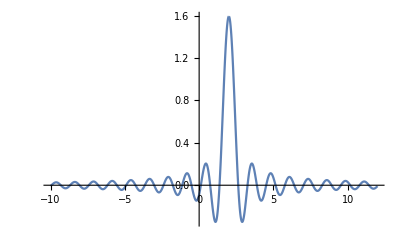

```mathematica
s[x_]:=Sin[g(x-a)]/(π(x-a));
a=2;g=5;
Plot[s[x],{x,-10,10+a},PlotRange->Full,PlotLegends->"Expressions"]
```

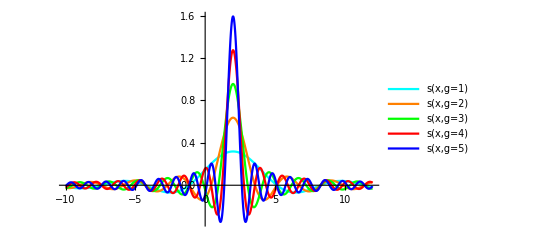

```mathematica
s[x_,g_]:=Sin[g(x-a)]/(π(x-a));
a=2;
Plot[{s[x,g=1],s[x,g=2],s[x,g=3],s[x,g=4],s[x,g=5]},{x,-10,10+a},PlotRange->Full,PlotStyle->{Cyan,Orange,Green,Red,Blue},PlotLegends->"Expressions"]
```

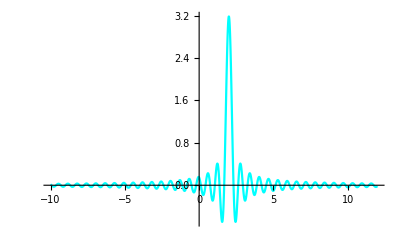

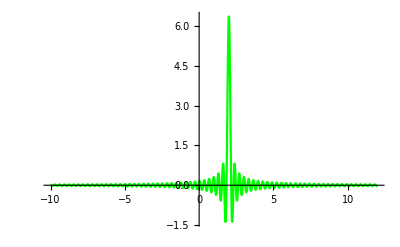

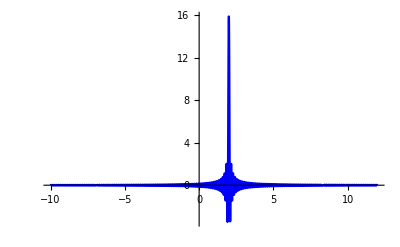

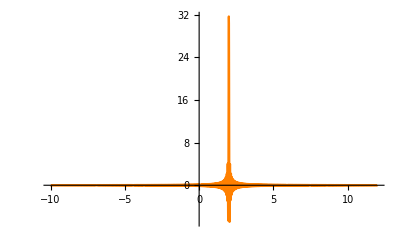

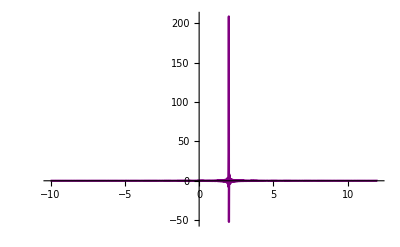

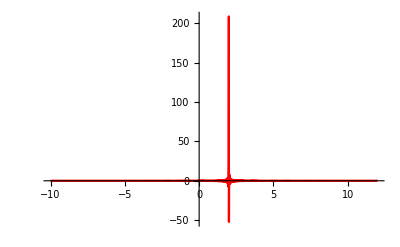

```mathematica
s[x_,g_]:=Sin[g(x-a)]/(π(x-a));
a=2;
Plot[s[x,g=10],{x,-10,10+a},PlotRange->Full,PlotStyle->Cyan,PlotLegends->"Expressions"]
Plot[s[x,g=20],{x,-10,10+a},PlotRange->Full,PlotStyle->Green]
Plot[s[x,g=50],{x,-10,10+a},PlotRange->Full,PlotStyle->Blue]
Plot[s[x,g=100],{x,-10,10+a},PlotRange->Full,PlotStyle->Orange]
Plot[s[x,g=1000],{x,-10,10+a},PlotRange->Full,PlotStyle->Purple]
Plot[s[x,g=1000],{x,-10,10+a},PlotRange->Full,PlotStyle->Red]
```